```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;Clear[κ];rep={a1->Subscript[a, 1],κi->Subscript[κ, i],κr->Subscript[κ, r],kx->Subscript[k, x], ky->Subscript[k, y], kz->Subscript[k, z], vz->Subscript[v, z], vp->Subscript[v, p],en->e,b1->Subscript[b, 1]};
ass=Assumptions->{en,k,θ,v,kx,ky,kz,κr,κi,k1,k2,kw}∈ Reals &&  k>0 && kp>0 && en>=0 && v>0 && vz>0 && kw>0;
sx=({{0, 1}, {1, 0}});sy=({{0, -ⅈ}, {ⅈ, 0}});sz=({{1, 0}, {0, -1}});
id=({{1, 0}, {0, 1}});{dx,dy,dz}={ ((*√3*)v(kx^2-ky^2))/2,(kx^2+ky^2-2 kz^2)/2,(*√3*) v kx ky kz};{ddx,ddy,ddz}={dx,dy,dz}/.{kx->k1+k2,ky->k1-k2}//FullSimplify;
```

## quad Weyl node

```mathematica
Clear[ham,eval];
(* -Graphics-; PRB B 106,134108 (2022) *)
ham=dx sx+dy sy+dz sz;
{ev,vec}=FullSimplify[Eigensystem[ham],ass]
```

{{-1/2 √((kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2)) v^2),1/2 √((kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2)) v^2)},{{-(ⅈ (-2 kx ky kz v+√((kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2)) v^2)))/(2 kz^2+ky^2 (-1-ⅈ v)+ⅈ kx^2 (ⅈ+v)),1},{(ⅈ (2 kx ky kz v+√((kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2)) v^2)))/(2 kz^2+ky^2 (-1-ⅈ v)+ⅈ kx^2 (ⅈ+v)),1}}}

```mathematica
eqq=(kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2)) v^2/.{kz->1/√2}
```

(-1+kx^2+ky^2)^2+(kx^4+ky^4) v^2

## FA

```mathematica
D[dx sigx+dy sigy+dz sigz,kx]/.kx->-ⅈ Dx
ComplexExpand[ReIm[%/.Dx->-(κr+ⅈ κi)]][[1]]//FullSimplify
```

-ⅈ Dx sigy-ⅈ Dx sigx v+ky kz sigz v

ky kz sigz v-(sigy+sigx v) κi

```mathematica
Clear[eq0,prod,v,cosa,sina,κ,κr,κi,a1,b1];
κ=κr+ⅈ κi;
ψ={1,a1+ⅈ b1};
ψdag={1,a1-ⅈ b1};
prod=FullSimplify[-κi (v ψdag.(sx.ψ)+ψdag.(sy.ψ))+v ky kz ψdag.(sz.ψ),ass];
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1]
```

{-((-1+a1^2+b1^2) ky kz v)-2 (b1+a1 v) κi,0}

```mathematica
dx sxψ+dy syψ+dz szψ/.kx->-ⅈ Dx//Expand
```

-(Dx^2 syψ)/2+(ky^2 syψ)/2-kz^2 syψ-1/2 Dx^2 sxψ v-1/2 ky^2 sxψ v-ⅈ Dx ky kz szψ v

```mathematica
Clear[eq,eqn,solu];
κ=κr+ ⅈ κi;a1=1/(√(1+v^2));b1=-v/(√(1+v^2));eq=2FullSimplify[-(κ^2 sy.ψ)/2+(ky^2 sy.ψ)/2-kz^2 sy.ψ-v/2 κ^2 sx.ψ-v/2 ky^2 sx.ψ+ⅈ v κ ky kz sz.ψ  -en id.ψ,ass]
(* -(Dx^2 syψ)/2+(ky^2 syψ)/2-kz^2 syψ-v/2 Dx^2 sxψ-v/2 ky^2 sxψ-ⅈ v Dx ky kz szψ *)
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1];
solu=FullSimplify[Solve[ eq0[[1]]==0&& eqn[[1]]==0  && eqn[[2]]==0 && eqn[[3]]==0  && eqn[[4]]==0 && κr≠0,{en,κr,κi}],ass]
Clear[ky,v,κr,κ,κi,a1,b1];
```

{2 (-en+(ⅈ ky^2 (ⅈ+v)^2+(ⅈ+v) (2 kz^2-ⅈ (-ⅈ+v) (κi-ⅈ κr)^2)-2 ky kz v √(1+v^2) (κi-ⅈ κr))/(2 √(1+v^2))),-2 ⅈ kz^2-ky^2 (-ⅈ+v)+(2 ⅈ en (ⅈ+v))/(√(1+v^2))+(2 ky kz (1-ⅈ v) v (κi-ⅈ κr))/(√(1+v^2))+(ⅈ+v) (κi-ⅈ κr)^2}

{{en→((-ky^2+kz^2) v)/(√(1+v^2)),κr→(-ky kz v-√(-2 kz^2+ky^2 (1+(-1+kz^2) v^2)))/(√(1+v^2)),κi→0},{en→((-ky^2+kz^2) v)/(√(1+v^2)),κr→(-ky kz v+√(-2 kz^2+ky^2 (1+(-1+kz^2) v^2)))/(√(1+v^2)),κi→0},{en→((-ky^2+kz^2) v)/(√(1+v^2)),κr→-(ky kz v)/(√(1+v^2)),κi→-√((2 kz^2+ky^2 (-1-(-1+kz^2) v^2))/(1+v^2))},{en→((-ky^2+kz^2) v)/(√(1+v^2)),κr→-(ky kz v)/(√(1+v^2)),κi→√((2 kz^2+ky^2 (-1-(-1+kz^2) v^2))/(1+v^2))}}

```mathematica
(* -Graphics- *)
```

```mathematica
(*{{en->((-ky^2+kz^2) v)/(√(1+v^2)),κr->-(ky kz v)/(√(1+v^2)),κi->-√((2 kz^2+ky^2 (-1-(-1+kz^2) v^2))/(1+v^2)),a1->1/(√(1+v^2)),b1->-v/(√(1+v^2))},

{en->((-ky^2+kz^2) v)/(√(1+v^2)),κr->-(ky kz v)/(√(1+v^2)),κi->√((2 kz^2+ky^2 (-1-(-1+kz^2) v^2))/(1+v^2)),a1->1/(√(1+v^2)),b1->-v/(√(1+v^2))},{en->((ky-kz) (ky+kz) v)/(√(1+v^2)),κr->(ky kz v)/(√(1+v^2)),κi->-√((2 kz^2+ky^2 (-1-(-1+kz^2) v^2))/(1+v^2)),a1->-1/(√(1+v^2)),b1->v/(√(1+v^2))},{en->((ky-kz) (ky+kz) v)/(√(1+v^2)),κr->(ky kz v)/(√(1+v^2)),κi->√((2 kz^2+ky^2 (-1-(-1+kz^2) v^2))/(1+v^2)),a1->-1/(√(1+v^2)),b1->v/(√(1+v^2))}}*)
```

```mathematica
(* where κr vanishes, what is the energy value? *)
FullSimplify[((-ky^2+kz^2) v)/(√(1+v^2))/.ky->0](* this is the right energy solution for μ>0*)
FullSimplify[((ky-kz) (ky+kz) v)/(√(1+v^2))/.kz->0](* this is the right energy solution for μ>0*)
```

(kz^2 v)/(√(1+v^2))

(ky^2 v)/(√(1+v^2))

```mathematica
(* maximum-radii FS-projections: *)
ensq=2((kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2)) v^2);
Solve[D[ensq,kx]==0,kx]
1/4((kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2)) v^2)/.kx->(√(-ky^2+2 kz^2+ky^2 v^2-2 ky^2 kz^2 v^2))/(√(1+v^2))//FullSimplify;
```

{{kx→0},{kx→-(√(-ky^2+2 kz^2+ky^2 v^2-2 ky^2 kz^2 v^2))/(√(1+v^2))},{kx→(√(-ky^2+2 kz^2+ky^2 v^2-2 ky^2 kz^2 v^2))/(√(1+v^2))}}

```mathematica
Clear[bulkentry, enfs];enfs=(v^2 (kz^4+2 ky^2 kz^2 (-1+kz^2)-ky^4 (-1+kz^2) (1+kz^2 v^2)))/(1+v^2);
bulkentry=DeleteDuplicates[FullSimplify[Solve[ (-(ky^2-kz^2) v)/(√(1+v^2))==μ && enfs==μ^2 && ky kz==0,{v,ky,kz}],ass]]
-ky kz/.bulkentry[[3]]
(* tangent value *)
FullSimplify[Grad[enfs,{ky,kz}]/.{ky->0,kz->pm (1+v^2)^(1/4) √(μ/v)},ass]/.pm^3->pm
Clear[v,μ];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ky→-ⅈ (1+v^2)^(1/4) √(μ/v),kz→0},{ky→ⅈ (1+v^2)^(1/4) √(μ/v),kz→0},{ky→0,kz→-(1+v^2)^(1/4) √(μ/v)},{ky→0,kz→(1+v^2)^(1/4) √(μ/v)}}

0

{0,(4 pm √v μ^(3/2))/((1+v^2)^(1/4))}

```mathematica
Clear[bulkentry];enfs=(v^2 (kz^4+2 ky^2 kz^2 (-1+kz^2)-ky^4 (-1+kz^2) (1+kz^2 v^2)))/(1+v^2);
bulkentry=DeleteDuplicates[FullSimplify[Solve[ ((ky^2-kz^2) v)/(√(1+v^2))==μ && enfs==μ^2 && ky kz==0,{v,ky,kz}],ass]]
ky kz/.bulkentry[[1]]
(* tangent value *)
FullSimplify[Grad[enfs,{ky,kz}]/.{kz->0,ky->pm (1+v^2)^(1/4) √(μ/v)},ass]/.pm^3->pm

Clear[v,μ];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ky→-(1+v^2)^(1/4) √(μ/v),kz→0},{ky→(1+v^2)^(1/4) √(μ/v),kz→0},{ky→0,kz→-ⅈ (1+v^2)^(1/4) √(μ/v)},{ky→0,kz→ⅈ (1+v^2)^(1/4) √(μ/v)}}

0

{(4 pm √v μ^(3/2))/((1+v^2)^(1/4)),0}

## Plot

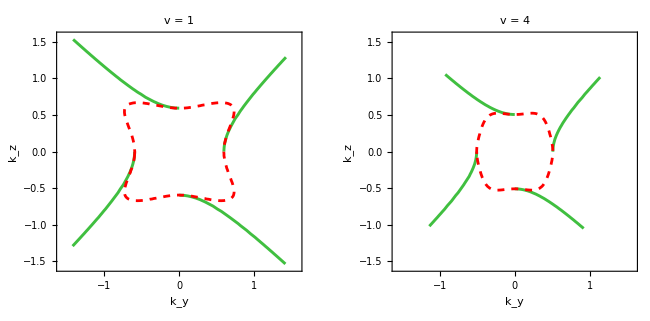

```mathematica
lim=π/2;mu=0.25;th=0.007;size=300;
style=Directive[Darker[Green],Thickness[th],Opacity[0.75]];
v=1;
ar1=Quiet[ContourPlot[((ky-kz) (ky+kz) v)/(√(1+v^2))==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style,RegionFunction->Function[{ky,kz,z},Chop[ky kz]>0 && 2 kz^2+ky^2 (-1+(1-kz^2) v^2)>=0],PlotLegends->Automatic,Contours->10]];
ar2=Quiet[ContourPlot[(-(ky-kz) (ky+kz) v)/(√(1+v^2))==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style,RegionFunction->Function[{ky,kz,z},Chop[-ky kz]>0 && 2 kz^2+ky^2 (-1+(1-kz^2) v^2)>=0],PlotLegends->Automatic,Contours->10]];
(***********)
kx=0;
fs0=ContourPlot[(kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2)) v^2==4mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->{Directive[Yellow,Dashing[0.0001]]}];
kx=(√2 √mu)/((1+v^2)^(1/4));
fsnz=ContourPlot[(kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2)) v^2==4mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->{Directive[Cyan,Dashing[0.0001]]}];
(* for kx=(√(-ky^2+2 kz^2+ky^2 v^2-2 ky^2 kz^2 v^2))/(√(1+v^2));*)
fs1=ContourPlot[(v^2 (kz^4+2 ky^2 kz^2 (-1+kz^2)-ky^4 (-1+kz^2) (1+kz^2 v^2)))/(1+v^2)==mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->{Directive[Red,Dashed]},RegionFunction->Function[{ky,kz,z},Chop[-ky^2+2 kz^2+ky^2 v^2-2 ky^2 kz^2 v^2]>=0]];
Show[ar1,ar2,fs0,fsnz,fs1,FrameLabel->{ky,kz}];
pl1=Show[ar1,ar2,fs1,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->size,PlotLabel->Style[(****)"v = 1",20,FontFamily->"TexMaths Symbols",Brown,Bold]];
(**************)
v=4;
ar1=Quiet[ContourPlot[((ky-kz) (ky+kz) v)/(√(1+v^2))==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style,RegionFunction->Function[{ky,kz,z},Chop[ky kz]>0 && 2 kz^2+ky^2 (-1+(1-kz^2) v^2)>=0],PlotLegends->Automatic,Contours->10]];
ar2=Quiet[ContourPlot[(-(ky-kz) (ky+kz) v)/(√(1+v^2))==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style,RegionFunction->Function[{ky,kz,z},Chop[-ky kz]>0 && 2 kz^2+ky^2 (-1+(1-kz^2) v^2)>=0],PlotLegends->Automatic,Contours->10]];
(***********)
fs1=ContourPlot[(v^2 (kz^4+2 ky^2 kz^2 (-1+kz^2)-ky^4 (-1+kz^2) (1+kz^2 v^2)))/(1+v^2)==mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->{Directive[Red,Dashed]},RegionFunction->Function[{ky,kz,z},Chop[-ky^2+2 kz^2+ky^2 v^2-2 ky^2 kz^2 v^2]>=0]];
pl2=Show[ar1,ar2,fs1,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->size,PlotLabel->Style[(****)"v =  4",20,FontFamily->"TexMaths Symbols",Brown,Bold]];
plt=GraphicsRow[{pl1,pl2}, ImageSize->650]
Clear[kx,v,a1,b1];
SetDirectory[NotebookDirectory[]];
Export["qweylarc.pdf",Rasterize[plt],ImageResolution->100];
```

## 2 nodes

{(4 v^2 ((kz-π)^4+2 (-1+(kz-π)^2) (kz-π)^2 (ky+π)^2-(-1+(kz-π)^2) (ky+π)^4 (1+(kz-π)^2 v^2)))/(1+v^2),2 (kz-π)^2-(ky+π)^2+(ky+π)^2 v^2-2 (kz-π)^2 (ky+π)^2 v^2}

{((ky+kz) (ky-kz+2 π) v)/(√(1+v^2)),-((kz-π) (ky+π)),2 (kz-π)^2+(ky+π)^2 (-1+(1-(kz-π)^2) v^2)≥0}

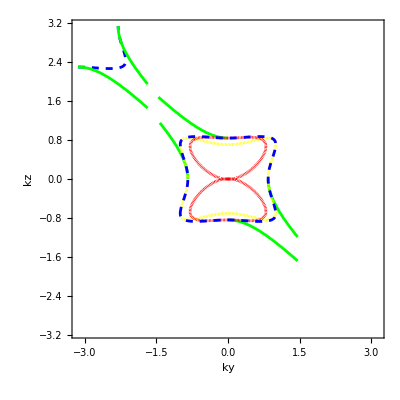

```mathematica
FullSimplify[{(4 v^2 (kz^4+2 ky^2 kz^2 (-1+kz^2)-ky^4 (-1+kz^2) (1+kz^2 v^2)))/(1+v^2),-ky^2+2 kz^2+ky^2 v^2-2 ky^2 kz^2 v^2}/.{kx->kx+π,ky->ky+π,kz->kz-π}]
(* *)
{((ky-kz) (ky+kz) v)/(√(1+v^2)),-ky kz,2 kz^2+ky^2 (-1+(1-kz^2) v^2)>=0}/.{kx->kx+π,ky->ky+π,kz->kz-π}
v=1;
arc2=Quiet[ContourPlot[((ky+kz) (ky-kz+2 π) v)/(√(1+v^2))==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Green,RegionFunction->Function[{ky,kz,z},Chop[-((kz-π) (ky+π))]>0 && 2 (kz-π)^2+(ky+π)^2 (-1+(1-(kz-π)^2) v^2)>=0],PlotLegends->Automatic,Contours->10]];
(***********)
arc3=Quiet[ContourPlot[(-(ky+kz) (ky-kz+2 π) v)/(√(1+v^2))==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Green,RegionFunction->Function[{ky,kz,z},Chop[-((kz-π) (ky+π))]>0 && 2 (kz-π)^2+(ky+π)^2 (-1+(1-(kz-π)^2) v^2)>=0],PlotLegends->Automatic,Contours->10]];
(******************)
fcorner=ContourPlot[(4 v^2 ((kz-π)^4+2 (-1+(kz-π)^2) (kz-π)^2 (ky+π)^2-(-1+(kz-π)^2) (ky+π)^4 (1+(kz-π)^2 v^2)))/(1+v^2)==4mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->{Directive[Blue,Dashed]},RegionFunction->Function[{ky,kz,z},Chop[2 (kz-π)^2-(ky+π)^2+(ky+π)^2 v^2-2 (kz-π)^2 (ky+π)^2 v^2]>=0]];
Show[sh1,fcorner,arc2,arc3]
Clear[v];
```

## FA 2: z surface

```mathematica
{ddx,ddy,ddz}
ddx sxψ+ddy syψ+ddz szψ/.kz->-ⅈ Dz//FullSimplify
```

{2 √3 kx ky,kx^2+ky^2-kz^2,√3 (kx-ky) (kx+ky) kz}

2 √3 kx ky sxψ+(Dz^2+kx^2+ky^2) syψ-ⅈ √3 Dz (kx-ky) (kx+ky) szψ

```mathematica
Clear[eq0,sol,M,cosa,sina,κ,κr,κi,a,c1,c2,a1,b1];
κi=0;
κ=κr+ⅈ κi;
ψ={1,a1+ⅈ b1};
ψdag={1,a1-ⅈ b1};
prod=-ⅈ FullSimplify[2ⅈ κi ( ψdag.(sy.ψ)+ψdag.(sy.ψ))-ⅈ √3(kx-ky) (kx+ky)  ψdag.(sz.ψ),ass];
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1]/√3
```

```mathematica
{(-1+a1^2+b1^2) (kx-ky) (kx+ky),0}
```

```mathematica
Clear[ψ,eq,eqn,solu];
ψ={1,a1+ⅈ b1};eq=(* 2 √3 kx ky sxψ+(Dz^2+kx^2+ky^2) syψ-ⅈ √3 Dz (kx-ky) (kx+ky) szψ *)2FullSimplify[2 √3 kx ky sx.ψ+(kx^2+ky^2) sy.ψ+ⅇ^(κ z)D[sy.ψ ⅇ^(-κ z),{z,2}]-ⅈ √3  (kx-ky) (kx+ky) ⅇ^(κ z)D[sz.ψ ⅇ^(-κ z),z]-en id.ψ,ass];
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1];
solu=FullSimplify[Solve[(*eq0[[1]]==0 &&*) eqn[[1]]==0  && eqn[[2]]==0  (*&& eqn[[3]]==0 && eqn[[4]]==0*) && κr≠0,{en,κr}],ass]
Clear[ky,α];
consis=FullSimplify[{(-1+a1^2+b1^2) (kx-ky) (kx+ky),a1^2 eqn[[3]],a1^2 eqn[[4]]}/.solu,ass]
```

## FA 2: k1 surface

```mathematica
{ddx,ddy,ddz}
ddx sxψ+ddy syψ+ddz szψ/.k1->-ⅈ Dk1//FullSimplify
```

{2 √3 k1 k2,k1^2+k2^2-kz^2,√3 (k1-k2) (k1+k2) kz}

-2 ⅈ √3 Dk1 k2 sxψ-kz^2 syψ+k2^2 (syψ-√3 kz szψ)-Dk1^2 (syψ+√3 kz szψ)

```mathematica
Clear[eq0,sol,M,cosa,sina,κ,κr,κi,a,c1,c2];
κi=0;
κ=κr+ⅈ κi;
ψ={1,a1+ⅈ b1};
ψdag={1,a1-ⅈ b1};
prod=ⅈ FullSimplify[-2 ⅈ √3  k2 ψdag.(sx.ψ)-2ⅈ κi ψdag.(sy.ψ+√3 kz sz.ψ),ass]/√3;
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1](*{√3 (-1+a1^2+b1^2) ky kz,0}*)
```

{4 a1 k2,0}

```mathematica
Clear[ψ,eq,eqn,b1,κr,en,solu];κ=κr;k2=0;
ψ={1,a1+ⅈ b1};eq=(* -2 ⅈ √3 Dx ky sxψ-kz^2 syψ+ky^2 (syψ-√3 kz szψ)-Dx^2 (syψ+√3 kz szψ)*)2FullSimplify[-2 ⅈ √3  k2 (-κ)sx.ψ-kz^2 sy.ψ+k2^2 (sy.ψ-√3 kz sz.ψ)-κ^2 (sy.ψ+√3 kz sz.ψ)-en id.ψ,ass];
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
sol=FullSimplify[Solve[eqn[[1]]==0 && eqn[[4]]==0 && κr≠0,{en,κr}],ass]
Length[sol]
Clear[ky,k2];
```

```mathematica
{-2 (en+b1 kz^2+(b1+√3 kz) κr^2),2 a1 (kz^2+κr^2),-2 a1 (en-√3 kz κr^2),-2 (kz^2+κr^2+b1 (en-√3 kz κr^2))}
```

```mathematica
{{en->-(√3 (1+b1^2) kz^3)/(-1+b1^2+2 √3 b1 kz),κr->-(√(-((-1+b1^2) (-1+√3 b1 kz))) Abs[kz])/(√(1+b1 (-b1+√3 (-3+b1^2) kz+6 b1 kz^2)))},{en->-(√3 (1+b1^2) kz^3)/(-1+b1^2+2 √3 b1 kz),κr->(√(-((-1+b1^2) (-1+√3 b1 kz))) Abs[kz])/(√(1+b1 (-b1+√3 (-3+b1^2) kz+6 b1 kz^2)))}}
```

2

```mathematica
Clear[ψ,eq,eqn,b1,κr,en,solu];κ=κr;
ψ=(*{1,Cos[α]+ⅈ Sin[α]}*){1,ⅈ b1};eq=(* -2 ⅈ √3 Dx ky sxψ-kz^2 syψ+ky^2 (syψ-√3 kz szψ)-Dx^2 (syψ+√3 kz szψ)*)2FullSimplify[-2 ⅈ √3  k2 (-κ)sx.ψ-kz^2 sy.ψ+k2^2 (sy.ψ-√3 kz sz.ψ)-κ^2 (sy.ψ+√3 kz sz.ψ)-en id.ψ,ass];
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
sol=FullSimplify[Solve[eqn[[1]]==0 && eqn[[4]]==0 && κr≠0,{en,κr}],ass]
Length[sol]
Clear[ky,α];
```

```mathematica
{-2 (en+√3 kz (k2^2+κr^2)+b1 (-k2^2+kz^2+2 √3 k2 κr+κr^2)),0,0,-2 (-k2^2+kz^2-2 √3 k2 κr+κr^2+b1 (en-√3 kz (k2^2+κr^2)))}
```

```mathematica
{{en->(-((1+b1^2) kz^3 (√3-9 b1 kz+3 b1^3 kz+√3 b1^2 (-1+6 kz^2)))+4 (1+b1^2) k2^2 (2 √3 kz+b1 (3+kz (-9 kz+6 b1^2 kz+√3 b1 (-5+3 kz^2))))+4 b1 k2 √(12 k2^2 (1+b1 kz (-2 √3+3 b1 kz)) (1+b1^4+b1^2 (1-3 kz^2))-3 (-1+b1^2) kz^2 (-1+b1 (b1+4 √3 kz+b1 kz (-15 kz+3 b1^2 kz+2 √3 b1 (-1+3 kz^2)))))+6 k2 kz √(4 k2^2 (1+b1 kz (-2 √3+3 b1 kz)) (1+b1^4+b1^2 (1-3 kz^2))-(-1+b1^2) kz^2 (-1+b1 (b1+4 √3 kz+b1 kz (-15 kz+3 b1^2 kz+2 √3 b1 (-1+3 kz^2)))))-6 b1^2 k2 kz √(4 k2^2 (1+b1 kz (-2 √3+3 b1 kz)) (1+b1^4+b1^2 (1-3 kz^2))-(-1+b1^2) kz^2 (-1+b1 (b1+4 √3 kz+b1 kz (-15 kz+3 b1^2 kz+2 √3 b1 (-1+3 kz^2))))))/((-1+b1^2+2 √3 b1 kz) (1+b1 (-b1+√3 (-3+b1^2) kz+6 b1 kz^2))),κr->((1+b1^2) k2 (√3-3 b1 kz)+√(4 k2^2 (1+b1^2+b1^4-3 b1^2 kz^2) (1+b1 kz (-2 √3+3 b1 kz))-(-1+b1^2) kz^2 (-1+b1 (b1+4 √3 kz+b1 kz (-15 kz+3 b1^2 kz+2 √3 b1 (-1+3 kz^2))))))/(1+b1 (-b1+√3 (-3+b1^2) kz+6 b1 kz^2))},{en->(-((1+b1^2) kz^3 (√3-9 b1 kz+3 b1^3 kz+√3 b1^2 (-1+6 kz^2)))+4 (1+b1^2) k2^2 (2 √3 kz+b1 (3+kz (-9 kz+6 b1^2 kz+√3 b1 (-5+3 kz^2))))-4 b1 k2 √(12 k2^2 (1+b1 kz (-2 √3+3 b1 kz)) (1+b1^4+b1^2 (1-3 kz^2))-3 (-1+b1^2) kz^2 (-1+b1 (b1+4 √3 kz+b1 kz (-15 kz+3 b1^2 kz+2 √3 b1 (-1+3 kz^2)))))-6 k2 kz √(4 k2^2 (1+b1 kz (-2 √3+3 b1 kz)) (1+b1^4+b1^2 (1-3 kz^2))-(-1+b1^2) kz^2 (-1+b1 (b1+4 √3 kz+b1 kz (-15 kz+3 b1^2 kz+2 √3 b1 (-1+3 kz^2)))))+6 b1^2 k2 kz √(4 k2^2 (1+b1 kz (-2 √3+3 b1 kz)) (1+b1^4+b1^2 (1-3 kz^2))-(-1+b1^2) kz^2 (-1+b1 (b1+4 √3 kz+b1 kz (-15 kz+3 b1^2 kz+2 √3 b1 (-1+3 kz^2))))))/((-1+b1^2+2 √3 b1 kz) (1+b1 (-b1+√3 (-3+b1^2) kz+6 b1 kz^2))),κr->((1+b1^2) k2 (√3-3 b1 kz)-√(4 k2^2 (1+b1^2+b1^4-3 b1^2 kz^2) (1+b1 kz (-2 √3+3 b1 kz))-(-1+b1^2) kz^2 (-1+b1 (b1+4 √3 kz+b1 kz (-15 kz+3 b1^2 kz+2 √3 b1 (-1+3 kz^2))))))/(1+b1 (-b1+√3 (-3+b1^2) kz+6 b1 kz^2))}}
```

2

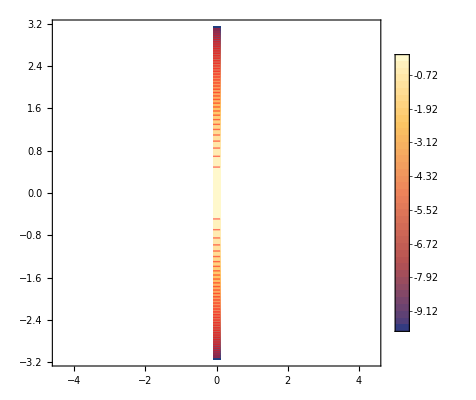

```mathematica
b1=1;ar3=Quiet[ContourPlot[-(√3 (1+b1^2) kz^3)/(-1+b1^2+2 √3 b1 kz),{k2,-√2 lim,√2 lim},{kz,-lim,lim},ContourStyle->Red,RegionFunction->Function[{k2,kz,z},√(((1-b1^2) (-1+√3 b1 kz))/(1+b1 (-b1+√3 (-3+b1^2) kz+6 b1 kz^2))) Abs[kz]>=0 && -10^-1<k2 && k2<10^-1 ],PlotLegends->Automatic,Contours->40]]
Clear[b1];
```

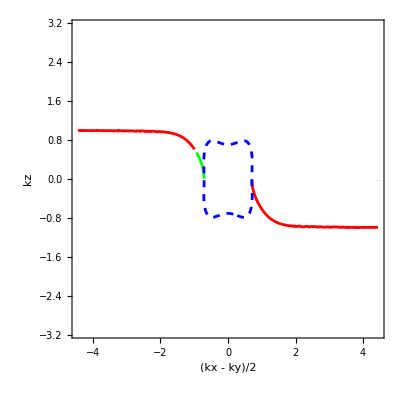

```mathematica
lim=π;mu=0.5;b1=1;
ar1=Quiet[ContourPlot[(-((1+b1^2) kz^3 (√3-9 b1 kz+3 b1^3 kz+√3 b1^2 (-1+6 kz^2)))+4 (1+b1^2) k2^2 (2 √3 kz+b1 (3+kz (-9 kz+6 b1^2 kz+√3 b1 (-5+3 kz^2))))+4 b1 k2 √(12 k2^2 (1+b1 kz (-2 √3+3 b1 kz)) (1+b1^4+b1^2 (1-3 kz^2))-3 (-1+b1^2) kz^2 (-1+b1 (b1+4 √3 kz+b1 kz (-15 kz+3 b1^2 kz+2 √3 b1 (-1+3 kz^2)))))+6 k2 kz √(4 k2^2 (1+b1 kz (-2 √3+3 b1 kz)) (1+b1^4+b1^2 (1-3 kz^2))-(-1+b1^2) kz^2 (-1+b1 (b1+4 √3 kz+b1 kz (-15 kz+3 b1^2 kz+2 √3 b1 (-1+3 kz^2)))))-6 b1^2 k2 kz √(4 k2^2 (1+b1 kz (-2 √3+3 b1 kz)) (1+b1^4+b1^2 (1-3 kz^2))-(-1+b1^2) kz^2 (-1+b1 (b1+4 √3 kz+b1 kz (-15 kz+3 b1^2 kz+2 √3 b1 (-1+3 kz^2))))))/((-1+b1^2+2 √3 b1 kz) (1+b1 (-b1+√3 (-3+b1^2) kz+6 b1 kz^2)))==mu,{k2,-√2 lim,√2 lim},{kz,-lim,lim},ContourStyle->Green,RegionFunction->Function[{k2,kz,z},Chop[((1+b1^2) k2 (√3-3 b1 kz)+√(4 k2^2 (1+b1^2+b1^4-3 b1^2 kz^2) (1+b1 kz (-2 √3+3 b1 kz))-(-1+b1^2) kz^2 (-1+b1 (b1+4 √3 kz+b1 kz (-15 kz+3 b1^2 kz+2 √3 b1 (-1+3 kz^2))))))/(1+b1 (-b1+√3 (-3+b1^2) kz+6 b1 kz^2))]>0 && -k2^2 (-1+kz^2)>=0 ],PlotLegends->Automatic,Contours->10]];
(**********)
ar2=Quiet[ContourPlot[(-((1+b1^2) kz^3 (√3-9 b1 kz+3 b1^3 kz+√3 b1^2 (-1+6 kz^2)))+4 (1+b1^2) k2^2 (2 √3 kz+b1 (3+kz (-9 kz+6 b1^2 kz+√3 b1 (-5+3 kz^2))))-4 b1 k2 √(12 k2^2 (1+b1 kz (-2 √3+3 b1 kz)) (1+b1^4+b1^2 (1-3 kz^2))-3 (-1+b1^2) kz^2 (-1+b1 (b1+4 √3 kz+b1 kz (-15 kz+3 b1^2 kz+2 √3 b1 (-1+3 kz^2)))))-6 k2 kz √(4 k2^2 (1+b1 kz (-2 √3+3 b1 kz)) (1+b1^4+b1^2 (1-3 kz^2))-(-1+b1^2) kz^2 (-1+b1 (b1+4 √3 kz+b1 kz (-15 kz+3 b1^2 kz+2 √3 b1 (-1+3 kz^2)))))+6 b1^2 k2 kz √(4 k2^2 (1+b1 kz (-2 √3+3 b1 kz)) (1+b1^4+b1^2 (1-3 kz^2))-(-1+b1^2) kz^2 (-1+b1 (b1+4 √3 kz+b1 kz (-15 kz+3 b1^2 kz+2 √3 b1 (-1+3 kz^2))))))/((-1+b1^2+2 √3 b1 kz) (1+b1 (-b1+√3 (-3+b1^2) kz+6 b1 kz^2)))==mu,{k2,-√2 lim,√2 lim},{kz,-lim,lim},ContourStyle->Red,RegionFunction->Function[{k2,kz,z},((1+b1^2) k2 (√3-3 b1 kz)-√(4 k2^2 (1+b1^2+b1^4-3 b1^2 kz^2) (1+b1 kz (-2 √3+3 b1 kz))-(-1+b1^2) kz^2 (-1+b1 (b1+4 √3 kz+b1 kz (-15 kz+3 b1^2 kz+2 √3 b1 (-1+3 kz^2))))))/(1+b1 (-b1+√3 (-3+b1^2) kz+6 b1 kz^2))>0 ],PlotLegends->Automatic,Contours->10]];
(* {en->-(√3 (1+b1^2) kz^3)/(-1+b1^2+2 √3 b1 kz),κr->(√(-((-1+b1^2) (-1+√3 b1 kz))) Abs[kz])/(√(1+b1 (-b1+√3 (-3+b1^2) kz+6 b1 kz^2)))}} *)
(*** {k1->(kx+ky)/2,k2->(kx-ky)/2}; k1^4+14 k1^2 k2^2+k2^4-2 k1^2 kz^2+3 k1^4 kz^2-2 k2^2 kz^2-6 k1^2 k2^2 kz^2+3 k2^4 kz^2+kz^4 **)
Clear[k2];
k1=0;
fs=ContourPlot[k1^4+14 k1^2 k2^2+k2^4-2 k1^2 kz^2+3 k1^4 kz^2-2 k2^2 kz^2-6 k1^2 k2^2 kz^2+3 k2^4 kz^2+kz^4==mu^2,{k2,-√2 lim,√2 lim},{kz,-lim,lim},Contours->20,ContourStyle->{Directive[Red,Dashed],Directive[Blue,Dashed]}];
Show[{ar1,ar2,fs},FrameLabel->{"(kx - ky)/2","kz"}]
Clear[kx,k1,b1];
```

## FA 2: k2 surface

```mathematica
{ddx,ddy,ddz}
ddx sxψ+ddy syψ+ddz szψ/.k2->-ⅈ Dk2//FullSimplify
```

{2 √3 k1 k2,k1^2+k2^2-kz^2,√3 (k1-k2) (k1+k2) kz}

-2 ⅈ √3 Dk2 k1 sxψ-kz^2 syψ+Dk2^2 (-syψ+√3 kz szψ)+k1^2 (syψ+√3 kz szψ)

```mathematica
Clear[eq0,sol,M,cosa,sina,κ,κr,κi,a,c1,c2];
κi=0;
κ=κr+ⅈ κi;
ψ={1,a1+ⅈ b1};
ψdag={1,a1-ⅈ b1};
prod=-ⅈ √3 FullSimplify[-2 ⅈ √3  k1 ψdag. (sx.ψ)+2ⅈ κ ψdag.(-sy.ψ+√3 kz sz.ψ),ass];
eq0=-Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1]/2
Solve[eq0[[1]]==0,b1]
```

```mathematica
{6 a1 k1+(2 √3 b1+3 (-1+a1^2) kz+3 b1^2 kz) κr,0}
```

```mathematica
{{b1->(-2 √3 κr-√(12 κr^2-12 kz κr (6 a1 k1-3 kz κr+3 a1^2 kz κr)))/(6 kz κr)},{b1->(-2 √3 κr+√(12 κr^2-12 kz κr (6 a1 k1-3 kz κr+3 a1^2 kz κr)))/(6 kz κr)}}
```

```mathematica
Clear[eq,eqn,solu,κr,a1];
(*κr=-(2 √3 a1 kx)/(2 b1-√3 kz+√3 (a1^2 + b1^2) kz);*)
eq=(* -2 ⅈ √3 Dy kx sxψ-kz^2 syψ+Dy^2 (-syψ+√3 kz szψ)+kx^2 (syψ+√3 kz szψ) *)2FullSimplify[-2 ⅈ √3 (-κ) k1 sx.ψ-kz^2 sy.ψ+κ^2 (-sy.ψ+√3 kz sz.ψ)+k1^2 (sy.ψ+√3 kz sz.ψ)-en id.ψ,ass];
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
solu=FullSimplify[Solve[eqn[[1]]==0 && eqn[[2]]==0  && eqn[[3]]==0 (*&& eqn[[4]]==0*) && κr≠0,{en,a1}],ass]
Clear[ky,α,κr,consis];
consis=FullSimplify[{6 a1 k1+(2 √3 b1+3 (-1+a1^2) kz+3 b1^2 kz)κr,eqn[[4]]/2}/.solu[[1]],ass];
solu2=FullSimplify[Solve[consis[[1]]==0 && consis[[2]]==0 && κr≠0,{κr, b1}],ass]
```

```mathematica
{-2 (en-√3 kz (k1^2+κr^2)+b1 (-k1^2+kz^2+2 √3 k1 κr+κr^2)),2 a1 (-k1^2+kz^2+2 √3 k1 κr+κr^2),-2 a1 (en+√3 kz (k1^2+κr^2)),-2 (-k1^2+kz^2-2 √3 k1 κr+κr^2+b1 (en+√3 kz (k1^2+κr^2)))}
```

```mathematica
{{en->b1 (k1^2-kz^2-2 √3 k1 κr-κr^2)+√3 kz (k1^2+κr^2),a1->0}}
```

```mathematica
{{κr->-(√3 k1+√(-kz^2+k1^2 (4-3 kz^2)))/(√(1+3 kz^2)),b1->-(1+√(1+3 kz^2))/(√3 kz)},{κr->(-√3 k1+√(-kz^2+k1^2 (4-3 kz^2)))/(√(1+3 kz^2)),b1->-(1+√(1+3 kz^2))/(√3 kz)},{κr->(√3 k1-√(-kz^2+k1^2 (4-3 kz^2)))/(√(1+3 kz^2)),b1->(-1+√(1+3 kz^2))/(√3 kz)},{κr->(√3 k1+√(-kz^2+k1^2 (4-3 kz^2)))/(√(1+3 kz^2)),b1->(-1+√(1+3 kz^2))/(√3 kz)}}
```

```mathematica
FullSimplify[{b1 (k1^2-kz^2-2 √3 k1 κr-κr^2)+√3 kz (k1^2+κr^2),κr,b1}/.solu2,ass]
```

{{(√3 kz (-2 k1^2+kz^2))/(√(1+3 kz^2)),-(√3 k1+√(-kz^2+k1^2 (4-3 kz^2)))/(√(1+3 kz^2)),-(1+√(1+3 kz^2))/(√3 kz)},{(√3 kz (-2 k1^2+kz^2))/(√(1+3 kz^2)),(-√3 k1+√(-kz^2+k1^2 (4-3 kz^2)))/(√(1+3 kz^2)),-(1+√(1+3 kz^2))/(√3 kz)},{-(√3 kz (-2 k1^2+kz^2))/(√(1+3 kz^2)),(√3 k1-√(-kz^2+k1^2 (4-3 kz^2)))/(√(1+3 kz^2)),(-1+√(1+3 kz^2))/(√3 kz)},{-(√3 kz (-2 k1^2+kz^2))/(√(1+3 kz^2)),(√3 k1+√(-kz^2+k1^2 (4-3 kz^2)))/(√(1+3 kz^2)),(-1+√(1+3 kz^2))/(√3 kz)}}

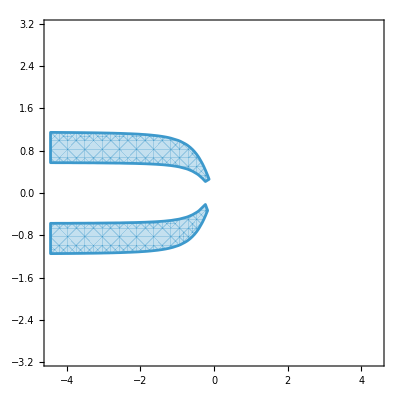

```mathematica
rp=RegionPlot[(-√3 k1-√(-kz^2+k1^2 (4-3 kz^2))>0  )&&(-√3 k1-√(-kz^2+k1^2 (4-3 kz^2))>0  )&& -kz^2+k1^2 (4-3 kz^2)>=0,{k1,-√2 lim,√2 lim},{kz,-lim,lim},PlotLegends->Automatic]//Quiet
```

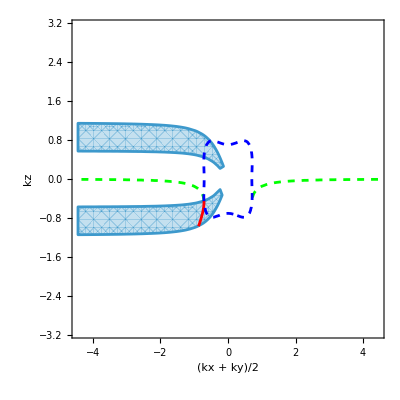

```mathematica
lim=π;mu=0.5;
ar1=Quiet[ContourPlot[(√3 kz (-2 k1^2+kz^2))/(√(1+3 kz^2))==mu,{k1,-√2 lim,√2 lim},{kz,-lim,lim},ContourStyle->Red,RegionFunction->Function[{k1,kz,z},(-√3 k1-√(-kz^2+k1^2 (4-3 kz^2))>0  )&& -kz^2+k1^2 (4-3 kz^2)>=0],PlotLegends->Automatic,Contours->10]];
ar3=Quiet[ContourPlot[(√3 kz (-2 k1^2+kz^2))/(√(1+3 kz^2))==mu,{k1,-√2 lim,√2 lim},{kz,-lim,lim},ContourStyle->Directive[Dashed,Green],RegionFunction->Function[{k1,kz,z},(-√3 k1+√(-kz^2+k1^2 (4-3 kz^2))>0 )&& -kz^2+k1^2 (4-3 kz^2)>=0 && (-√3 k1-√(-kz^2+k1^2 (4-3 kz^2))<0  )],PlotLegends->Automatic,Contours->10]];
(*************)

Clear[k2];
k2=0;
fs=ContourPlot[k1^4+14 k1^2 k2^2+k2^4-2 k1^2 kz^2+3 k1^4 kz^2-2 k2^2 kz^2-6 k1^2 k2^2 kz^2+3 k2^4 kz^2+kz^4==mu^2,{k1,-√2 lim,√2 lim},{kz,-lim,lim},Contours->20,ContourStyle->{Directive[Red,Dashed],Directive[Blue,Dashed]}];
Show[{rp,ar1,ar3,fs},FrameLabel->{"(kx + ky)/2","kz"}]
Clear[kx,ky,k1,k2,α];
```

```mathematica
lim=1;ContourPlot3D[{k1^4+14 k1^2 k2^2+k2^4-2 k1^2 kz^2+3 k1^4 kz^2-2 k2^2 kz^2-6 k1^2 k2^2 kz^2+3 k2^4 kz^2+kz^4==0.25,k2==0},{k1,-√2 lim,√2 lim},{k2,-√2 lim,√2 lim},{kz,-lim,lim},Mesh->Full,AxesLabel->{k1,k2,kz},ViewPoint->{0.5094433778954321,-3.073711932854777,1.320137265038998}]
```

-Graphics3D-

```mathematica
lim=1;

k2=0;p1=Plot3D[{√(k1^4+14 k1^2 k2^2+k2^4-2 k1^2 kz^2+3 k1^4 kz^2-2 k2^2 kz^2-6 k1^2 k2^2 kz^2+3 k2^4 kz^2+kz^4),-√(k1^4+14 k1^2 k2^2+k2^4-2 k1^2 kz^2+3 k1^4 kz^2-2 k2^2 kz^2-6 k1^2 k2^2 kz^2+3 k2^4 kz^2+kz^4)},{k1,-√2 lim,√2 lim},{kz,-lim,lim},BoxRatios->{1, 1, 1}];
k2=0.5;p2=Plot3D[{√(k1^4+14 k1^2 k2^2+k2^4-2 k1^2 kz^2+3 k1^4 kz^2-2 k2^2 kz^2-6 k1^2 k2^2 kz^2+3 k2^4 kz^2+kz^4),-√(k1^4+14 k1^2 k2^2+k2^4-2 k1^2 kz^2+3 k1^4 kz^2-2 k2^2 kz^2-6 k1^2 k2^2 kz^2+3 k2^4 kz^2+kz^4)},{k1,-√2 lim,√2 lim},{kz,-lim,lim},BoxRatios->{1, 1, 1}];
k2=-0.5;p3=Plot3D[{√(k1^4+14 k1^2 k2^2+k2^4-2 k1^2 kz^2+3 k1^4 kz^2-2 k2^2 kz^2-6 k1^2 k2^2 kz^2+3 k2^4 kz^2+kz^4),-√(k1^4+14 k1^2 k2^2+k2^4-2 k1^2 kz^2+3 k1^4 kz^2-2 k2^2 kz^2-6 k1^2 k2^2 kz^2+3 k2^4 kz^2+kz^4)},{k1,-√2 lim,√2 lim},{kz,-lim,lim},BoxRatios->{1, 1, 1}];
{p1,p2,p3}
Clear[kx,ky,k1,k2,α];
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

## FA2: Numerical soln

```mathematica
Clear[dat];
dat[μ_,pts_]:=Module[{κr,κi=0,k1,kz,eq0,eqn,en=μ,a1,b1,del=2π/pts,i,j,dat={},sol,len},
eq0=6 a1 k1+(2 √3 b1+3 (-1+a1^2) kz+3 b1^2 kz) κr;
eqn={-2 (en-√3 kz (k1^2+κr^2)+b1 (-k1^2+kz^2+2 √3 k1 κr+κr^2)),2 a1 (-k1^2+kz^2+2 √3 k1 κr+κr^2),-2 a1 (en+√3 kz (k1^2+κr^2)),-2 (-k1^2+kz^2-2 √3 k1 κr+κr^2+b1 (en+√3 kz (k1^2+κr^2)))};
For[(**)i=0,i<=pts,i++,
kz=-π*1.0+i del;
sol=Chop[Quiet[NSolveValues[eq0==0 && eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0  && Re[κr]>0 &&  Abs[Im[κr]]<10^-6,{k1,κr,a1,b1}]],10^-6];
len=Length[sol];
For[j=1,j<=len,j++,dat=AppendTo[dat,{sol[[j,1]],kz}](*; Print["***********"]*)]
(**)];
Sort[dat]];
(*lim=π;mu=0.5;
ydat=dat[mu,40]*)
```

```mathematica
Clear[datp];
datp[μ_,pts_]:=Module[{κr,κi=0,k1,kz,eq0,eqn,en=μ,a1,b1,del=2π/pts,i,j,dat={},sol,len},
eq0=6 a1 k1+(2 √3 b1+3 (-1+a1^2) kz+3 b1^2 kz) κr;
eqn={-2 (en-√3 kz (k1^2+κr^2)+b1 (-k1^2+kz^2+2 √3 k1 κr+κr^2)),2 a1 (-k1^2+kz^2+2 √3 k1 κr+κr^2),-2 a1 (en+√3 kz (k1^2+κr^2)),-2 (-k1^2+kz^2-2 √3 k1 κr+κr^2+b1 (en+√3 kz (k1^2+κr^2)))};
For[(**)i=0,i<=pts,i++,
k1=-π*1.0+i del;
sol=Chop[Quiet[NSolveValues[eq0==0 && eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0  && Re[κr]>0 &&  Abs[Im[κr]]<10^-6,{kz,κr,a1,b1}]],10^-6];
len=Length[sol];
For[j=1,j<=len,j++,dat=AppendTo[dat,{k1,sol[[j,1]]}](*; Print["***********"]*)]
(**)];
Sort[dat]];
lim=π;mu=0.5;
xdat=datp[mu,40]
```

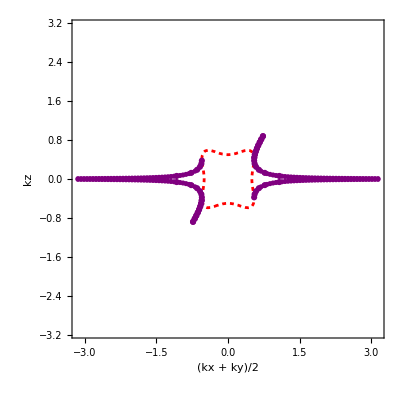

```mathematica
lim=π;mu=0.25;
(*ydat=dat[mu,100];xdat=datp[mu,100];*)
ar1=ListPlot[{ydat},PlotRange->{-π,π},Frame->True,PlotStyle->Purple];
ar2=ListPlot[{xdat},PlotRange->{-π,π},Frame->True,PlotStyle->Purple];

Clear[k2];
k2=0;
fs=ContourPlot[k1^4+14 k1^2 k2^2+k2^4-2 k1^2 kz^2+3 k1^4 kz^2-2 k2^2 kz^2-6 k1^2 k2^2 kz^2+3 k2^4 kz^2+kz^4==mu^2,{k1,-lim,lim},{kz,-lim,lim},Contours->20,ContourStyle->{Directive[Red,Dashing[0.007]]}];
Show[{fs,ar1,ar2},FrameLabel->{"(kx + ky)/2","kz"}]
Clear[k1,mu];
```

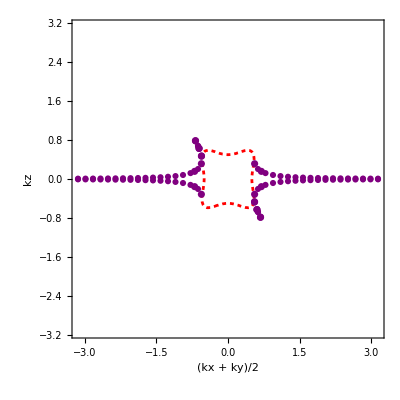

```mathematica
lim=π;mu=-0.25;
ydat=dat[mu,40];xdat=datp[mu,40];
ar1=ListPlot[{ydat},PlotRange->{-π,π},Frame->True,PlotStyle->Purple];
ar2=ListPlot[{xdat},PlotRange->{-π,π},Frame->True,PlotStyle->Purple];

Clear[k2];
k2=0;
fs=ContourPlot[k1^4+14 k1^2 k2^2+k2^4-2 k1^2 kz^2+3 k1^4 kz^2-2 k2^2 kz^2-6 k1^2 k2^2 kz^2+3 k2^4 kz^2+kz^4==mu^2,{k1,-lim,lim},{kz,-lim,lim},Contours->20,ContourStyle->{Directive[Red,Dashing[0.007]]}];
Show[{fs,ar1,ar2},FrameLabel->{"(kx + ky)/2","kz"}]
Clear[k1,mu];
```

## disp about R point

```mathematica
(* -Graphics- ; {dx,dy,dz}={ ((*√3*)v(kx^2-ky^2))/2,(kx^2+ky^2-2 kz^2)/2,(*√3*) v kx ky kz};*)
{kx,ky,kz}={π+qx,π+qy,π+qz};exp=(*0(Cos[kx]+Cos[ky]+Cos[kz])id*){2 √3(Cos[ky]-Cos[kx]),-(*√3*)v(Cos[ky]+Cos[kx]-2Cos[kz]), Sin[kx]Sin[ky]Sin[kz]};
Series[exp,{qx,0,2},{qy,0,2},{qz,0,2}]//FullSimplify//Normal
Clear[kx,ky,kz];
```

{-√3 qx^2+√3 qy^2,-(qx^2 v)/2-(qy^2 v)/2+qz^2 v,-qx qy qz}

```mathematica
{kx,ky,kz}={qx,qy,qz};exp=0(Cos[kx]+Cos[ky]+cos[kz])id+2 √3(Cos[ky]-Cos[kx])sx-2 √3(Cos[ky]+Cos[kx]-2Cos[kz])sz+c3 Sin[kx]Sin[ky]Sin[kz];
ser=Series[exp,{qx,0,2},{qy,0,2},{qz,0,2}]//FullSimplify//Normal
ser/.{qx->kx-π,qy->ky-π,qz->kz-π}//FullSimplify
```

{{√3 qx^2+√3 qy^2+c3 qx qy qz-2 √3 qz^2,√3 qx^2-√3 qy^2+c3 qx qy qz},{√3 qx^2-√3 qy^2+c3 qx qy qz,-√3 qx^2-√3 qy^2+c3 qx qy qz+2 √3 qz^2}}

{{-c3 (π-qx) (π-qy) (π-qz)+√3 (qx^2+qy^2-2 π (qx+qy-2 qz)-2 qz^2),√3 (-2 π qx+qx^2+2 π qy-qy^2)-c3 (π-qx) (π-qy) (π-qz)},{√3 (-2 π qx+qx^2+2 π qy-qy^2)-c3 (π-qx) (π-qy) (π-qz),-c3 (π-qx) (π-qy) (π-qz)+√3 (-qx^2-qy^2+2 π (qx+qy-2 qz)+2 qz^2)}}

```mathematica
lim=-π;Clear[kx,ky,kz];repl={kx->0,ky->-ky-lim,kz->kz+lim};feq=kx^4+ky^4-ky^2 kz^2+kz^4+kx^2 (-kz^2+ky^2 (-1+3 kz^2))/.repl
arceq=(√3)/2(ky-kz) (ky+kz)/.repl
coneq0=ky kz/.repl
coneq=2 kz^2+ky^2 (2-3 kz^2)/.repl
```

(kz-π)^4-(kz-π)^2 (-ky+π)^2+(-ky+π)^4

1/2 √3 (-ky+kz) (-ky-kz+2 π)

(kz-π) (-ky+π)

2 (kz-π)^2+(2-3 (kz-π)^2) (-ky+π)^2

```mathematica
lim=π;mu=0.4;
(* ar1=Quiet[ContourPlot[(√3)/2(ky-kz) (ky+kz)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Green,RegionFunction->Function[{ky,kz,z},Chop[ ky kz]>0 && 2 kz^2+ky^2 (2-3 kz^2)>=0],PlotLegends->Automatic,Contours->10]]; *)
ar1=Quiet[ContourPlot[arceq==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Directive[Dashed,Green],RegionFunction->Function[{ky,kz,z},Chop[coneq0]>0 && coneq>=0 ],PlotLegends->Automatic,Contours->10]];
(*****{en->1/2 √3 (-ky^2+kz^2),κr->-1/2 √3 ky kz,κi->1/2 √(2 kz^2+ky^2 (2-3 kz^2)),a1->1/2,b1->-(√3)/2},*)
fs=ContourPlot[feq==mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->{Directive[Red,Dashed],Directive[Blue,Dashed]}];
Show[ar1,fs,sh1]
Clear[kx,th,a1,b1];
```